# Assignment 3

## Group 4

Jordan Earle - 12297127, Martin Frassek - 12236632

## Introduction

Here is an introduction

## Exercise 1

### Background and Theory

Hi this is text

### Results and Discussion

#### A1

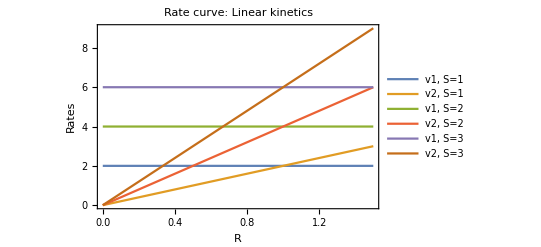

```mathematica
rateconsta = {k1 -> 2, k2 -> 2, k3 -> 1, k4 -> 1};
x = k3*s/k4;
ratesa = {v1 -> k1*s, v2 -> k2*x*r};

Plot[{
v1/.ratesa/.rateconsta/.s->1,
v2/.ratesa/.rateconsta/.s->1,
v1/.ratesa/.rateconsta/.s->2,
v2/.ratesa/.rateconsta/.s->2,
v1/.ratesa/.rateconsta/.s->3,
v2/.ratesa/.rateconsta/.s->3},

{r,0,1.5},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1, S=1", "v2, S=1", "v1, S=2", "v2, S=2", "v1, S=3", "v2, S=3"}, 
PlotLabel->Style["Rate curve: Linear kinetics", FontSize->18] ]
```

You can plot it and it would show  a constant response independent of the signal, which will be approximately 1.

#### A2

Floor[t/4]

{{x[t]→InterpolatingFunction[…][t],r[t]→InterpolatingFunction[…][t]}}

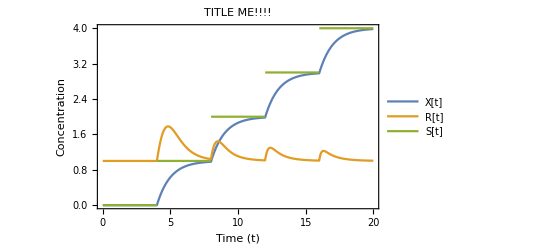

```mathematica
ClearAll["Global`*"];

s[t_] = Floor[t/4]

sol = NDSolve[Evaluate[{x'[t] == (1*s[t]) - (1*x[t]), r'[t] == (2*s[t]) - (2*x[t]*r[t]),r[0] == 1,x[0] == 0}], {x[t], r[t]}, {t, 0, 20}]
Plot[{x[t]/.sol, r[t]/.sol, s[t]}, {t,0,20},
Frame->True,FrameLabel->{"Time (t)","Concentration"},
PlotLegends -> {"X[t]","R[t]","S[t]"},
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

#### B1

Negative Feedback

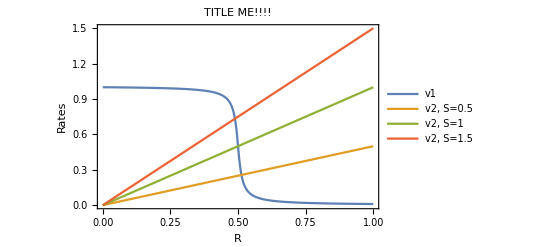

```mathematica
ClearAll["Global`*"];

G[u_, v_, J_, K_] := (2*u*K)/ (v-u+v*J+u*K+√((v-u+v*J+u*K)^2 - 4(v-u)*u*K))

rateconstb = {k0 -> 1, k2 -> 1, k3 -> 0.5, k4 -> 1, J3 -> 0.01, J4 -> 0.01 };

ratesb = {v1 -> k0*G[k3,k4*R,J3,J4]/.rateconstb, v2 -> k2*S*R};

Plot[{
v1/.ratesb/.rateconstb,
v2/.ratesb/.rateconstb/.S->0.5,
v2/.ratesb/.rateconstb/.S->1,
v2/.ratesb/.rateconstb/.S->1.5,
},

{R,0,1},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1", "v2, S=0.5", "v2, S=1", "v2, S=1.5"}, 
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

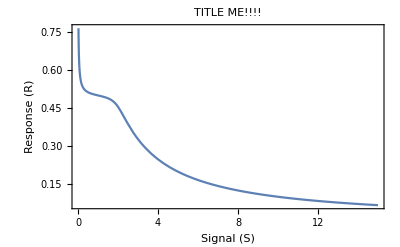

```mathematica
solb = Solve[0 == (v1-v2)/.ratesb,R][[1]][[1]][[2]];
Plot[solb/.rateconstb, 
{S,0,15},Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, 
(*PlotLegends -> {"v1", "v2, S=0.5", "v2, S=1", "v2, S=1.5"}, *)
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

Positive feedback: Mutual Inhibition

S

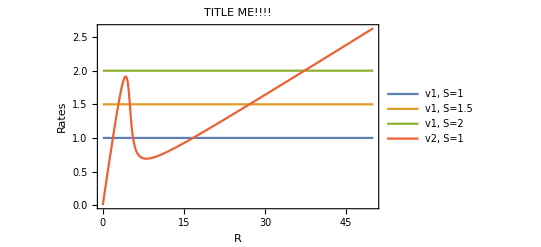

```mathematica
rateconstc = {k0 -> 0, k1 -> 1, k2 -> 0.05, k2nd -> 0.5, k3 -> 1, k4 -> 0.2, J3 -> 0.05, J4 -> 0.05};

ratesc = {v1 -> k0 + k1*S, v2 -> k2*R + k2nd*R*G[k3,k4*R,J3,J4]/.rateconstc};

v1/.ratesc/.rateconstc(*/.S->1*)

Plot[{
v1/.ratesc/.rateconstc/.S->1,
v1/.ratesc/.rateconstc/.S->1.5,
v1/.ratesc/.rateconstc/.S->2,
v2/.ratesc/.rateconstc
},

{R,0,50},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1, S=1", "v1, S=1.5", "v1, S=2", "v2, S=1", "v2, S=1.5", "v2, S=2"}, 
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

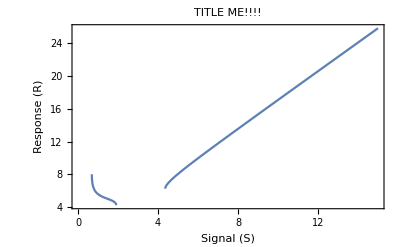

```mathematica
solc = Solve[0 == (v1-v2)/.ratesc,R][[1]][[1]][[2]];
Plot[solc/.rateconstc, 
{S,0,15},Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, 
(*PlotLegends -> {"v1", "v2, S=0.5", "v2, S=1", "v2, S=1.5"}, *)
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

Positive Feedback: Mutual Activation

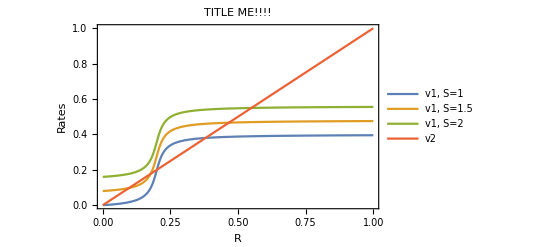

```mathematica
rateconstd = {k0 -> 0.4, k1 -> 0.01, k2 -> 1, k3 -> 1, k4 -> 0.2, J3 -> 0.05, J4 -> 0.05};

ratesd = {v1 -> k0*G[k3*R, k4, J3, J4]+k1*S, v2 -> k2*R};

Plot[{
v1/.ratesd/.rateconstd/.S->0,
v1/.ratesd/.rateconstd/.S->8,
v1/.ratesd/.rateconstd/.S->16,
v2/.ratesd/.rateconstd
},

{R,0,1},Frame->True,FrameLabel->{"R","Rates"}, 
PlotLegends -> {"v1, S=1", "v1, S=1.5", "v1, S=2", "v2"}, 
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

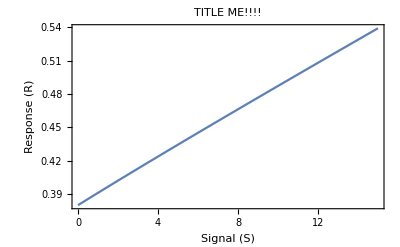

```mathematica
sold = Solve[0 == (v1-v2)/.ratesd,R][[1]][[1]][[2]];
Plot[sold/.rateconstd, 
{S,0,15},Frame->True,FrameLabel->{"Signal (S)","Response (R)"}, 
(*PlotLegends -> {"v1", "v2, S=0.5", "v2, S=1", "v2, S=1.5"}, *)
PlotLabel->Style["TITLE ME!!!!", FontSize->18]]
```

B1.b
Explain why in the homeostatic system, graphs 1, the response values are confined to a narrow window.....  They dont appear to be....

## Exercise 2

## Exercise 3